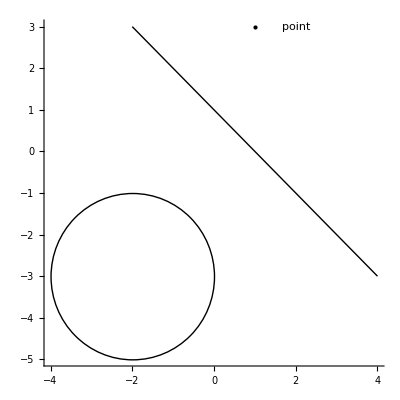

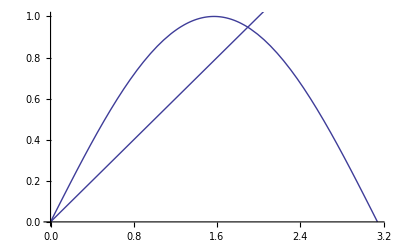

```mathematica
(* Here I will show you how to make some plots. Afterwards we will put
them into a LaTeX document *)
(* First an example with point, line, circle, text*)
Clear["`*"];
point=Point[{1,3}];
line=Line[{start,end}];
start={-2,3};end={4,-3};
circle=Circle[center,radius];
center={-2,-3};radius=2;
text=Text["point",{2,3}];
plot1=Graphics[{text,point,line,circle},AspectRatio->Automatic,Axes->True];(* To draw axes are not default for the command Graphics. Note also ;at the end. The plot comes with the Show command next*)
Show[plot1]
(* How to get this pliot into your LaTeX-document? Do you se the bracket
to the very right of the figure? Click on that one. Under File you select Save Selection As. In box Save As Type I choose EPS and give it a name, here plot1, and Save. Important that your eps file and your tex-file are in the same folder. Maybe you can save it as pdf. I will check that*)
(* Next I show how to combine plots by Show command *)
(* plot 4 is saved as an EPS file in the same way as plot1*)
plot2=Plot[Sin[x],{x,0,Pi}];
plot3=Plot[x/2,{x,0,Pi}];
plot4=Show[plot2,plot3]
```